```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
inh[x_,b_]:=b^2/(b^2 +x^2)
act[x_,a_]:=x^2/(a^2 + x^2)
```

```mathematica
u=0;
a1=0.6;a2=0.2;a3=0.2;a4=0.5;
b1=0.4;b2=0.7;b3=0.3;b4=0.5;b5=0.4;
```

```mathematica
NSolve[{-x1 + 0.5 (inh[x3,b4] act[u,a1] + act[x2,a3])==0,-x2 + act[x1,a2] inh[x3,b3]==0,-x3 + inh[x2,b2] inh[x4,b5]==0,
-x4 + 0.5 (inh[u,b1] + act[x3,a4])==0,1>a1>0,1>a2>0,1>a3>0,1>a4>0,1>b1>0,1>b2>0,1>b3>0,1>b4>0,1>b5>0},{x1,x2,x3,x4},Reals]
```

{{x1→0.0954598,x2→0.0971537,x3→0.286151,x4→0.62336},{x1→0.,x2→0.,x3→0.290008,x4→0.625866},{x1→0.447517,x2→0.584017,x3→0.196087,x4→0.566649}}

```mathematica
DSolve[{x1'[t]==-x1[t] + 0.5 (inh[x3[t],b4] act[u,a1] + act[x2[t],a3]),x2'[t]==-x2[t] + act[x1[t],a2] inh[x3[t],b3],x3'[t]==-x3[t] + inh[x2[t],b2] inh[x4[t],b5],
x4'[t]==-x4[t] + 0.5 (inh[u,b1] + act[x3[t],a4]),x1[0]==0,x2[0]==0,x3[0]==0.29,x4[0]==0.625},{x1,x2,x3,x4},t]
```

DSolve[{x1'[t]==-x1[t]+0.5 (0.+x2[t]^2/(0.04+x2[t]^2)),x2'[t]==-x2[t]+(0.09 x1[t]^2)/((0.04+x1[t]^2) (0.09+x3[t]^2)),x3'[t]==-x3[t]+0.0784/((0.49+x2[t]^2) (0.16+x4[t]^2)),x4'[t]==0.5 (1.+x3[t]^2/(0.25+x3[t]^2))-x4[t],x1[0]==0,x2[0]==0,x3[0]==0.29,x4[0]==0.625},{x1,x2,x3,x4},t]

## Target distribution

```mathematica
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->18},LabelStyle->Black};
```

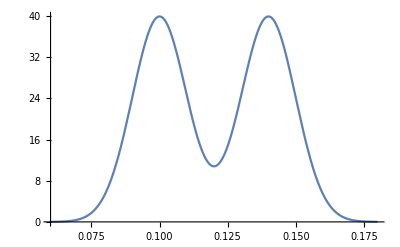

```mathematica
Plot[PDF[NormalDistribution[0.1,0.01],x]+PDF[NormalDistribution[0.14,0.01],x],{x,0.06,0.18}]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,0.005],x],{x,-0.02,0.02},Axes->None,PlotStyle->Blue,Filling->Bottom,FillingStyle->Opacity[0.7,Blue],AspectRatio->1/4,PlotRange->{Automatic,{0,81}}];
aPlot2=Plot[1/2 (PDF[NormalDistribution[-0.045,0.028],x]+PDF[NormalDistribution[0.045,0.028],x]),{x,-0.12,0.12},Axes->None,PlotStyle->Blue,Filling->Bottom,FillingStyle->Opacity[0.7,Blue],AspectRatio->1/2,PlotRange->{Automatic,{0,21}}];
aPlot3=Plot[1/2 (PDF[NormalDistribution[-0.12,0.01],x]+PDF[NormalDistribution[0.12,0.01],x]),{x,-0.14,0.14},Axes->None,PlotStyle->Blue,Filling->Bottom,FillingStyle->Opacity[0.7,Blue],AspectRatio->1/2,PlotRange->{Automatic,{0,31}}];
aPlot4=Plot[0.5 PDF[NormalDistribution[0,0.005],x],{x,-0.025,0.025},Axes->None,PlotStyle->Blue,Filling->Bottom,FillingStyle->Opacity[0.7,Blue],AspectRatio->1/4,PlotRange->{Automatic,{0,51}}];
```

```mathematica
g1=Show[ListPlot[Thread[{1,1}],PlotStyle->{{Thickness[0.01],Opacity[1,White]},{Thickness[0.01],Orange},{Thickness[0.01],Magenta}},PlotRange->{{0.7,4.5},{0,0.3}},Evaluate@options3,PlotMarkers ->{Automatic,15},FrameLabel->{"Time","[C3a]"},ImageSize->800],Graphics[Inset[Rotate[aPlot1,3Pi /2],{1,0.0625}]],Graphics[Inset[Rotate[aPlot2,3Pi /2],{2.1,0.12}]],Graphics[Inset[Rotate[aPlot4,3Pi /2],{4,0.2}]],Graphics[Inset[Rotate[aPlot4,3Pi /2],{4,0.1}]]]
```

-Graphics-

## Plot trajectories of [C3a] for accepted samples

```mathematica
samples=Import["../data/tnf_parameters.csv"];
samples=DeleteDuplicates@samples;
```

```mathematica
fSolve[params__]:=Block[{a1=params[[1]],a2=params[[2]],a3=params[[3]],a4=params[[4]],
b1=params[[5]],b2=params[[6]],b3=params[[7]],b4=params[[8]],b5=params[[9]],u,solns},u[t_]:=If[2≥t≥ 0.01, 1,0];
solns=NDSolve[{x1'[t]==-x1[t] + 0.5 (inh[x3[t],b4] act[u[t],a1] + act[x2[t],a3]),x2'[t]==-x2[t] + act[x1[t],a2] inh[x3[t],b3],x3'[t]==-x3[t] + inh[x2[t],b2] inh[x4[t],b5],
x4'[t]==-x4[t] + 0.5 (inh[u[t],b1] + act[x3[t],a4]),x1[0]==0,x2[0]==0,x3[0]==0.29,x4[0]==0.625},{x1,x2,x3,x4},{t,0,5}];solns[[1,2,2]]]
```

```mathematica
data=Table[Table[Evaluate[{t,fSolve[samples[[i]]][t]}],{t,0,5,0.05}],{i,1,Length@samples,1}];
```

```mathematica
g2=Show[ListLinePlot[data,PlotStyle->Opacity[0.2,Black],Evaluate@options3,FrameLabel->{"Time","[C3a]"},ImageSize->800,PlotRange->{Automatic,{0.,0.3}}],g1]
```

-Graphics-

## Trying to be exact with figure

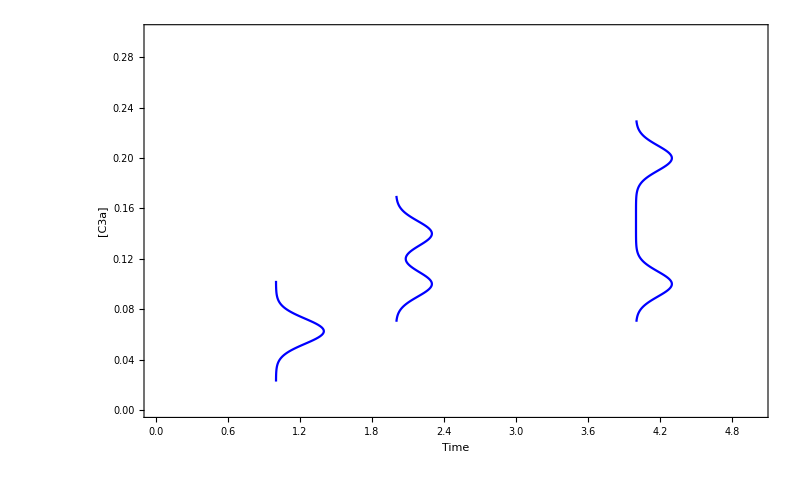

```mathematica
multiplier=0.015;
g3=ListLinePlot[{Table[{1+ 0.01PDF[NormalDistribution[0.0625,0.01],x],x},{x,0.0625-0.04,0.0625+0.04,0.001}],Table[{2+0.5 multiplier( PDF[NormalDistribution[0.1,0.01],x]+PDF[NormalDistribution[0.14,0.01],x]),x},{x,0.12-0.05,0.12+0.05,0.001}],Table[{4+0.5 multiplier( PDF[NormalDistribution[0.1,0.01],x]+PDF[NormalDistribution[0.2,0.01],x]),x},{x,0.15-0.08,0.15+0.08,0.001}]},Evaluate@options3,FrameLabel->{"Time","[C3a]"},ImageSize->800,PlotRange->{{0,5},{0.,0.3}},PlotStyle->Blue]
```

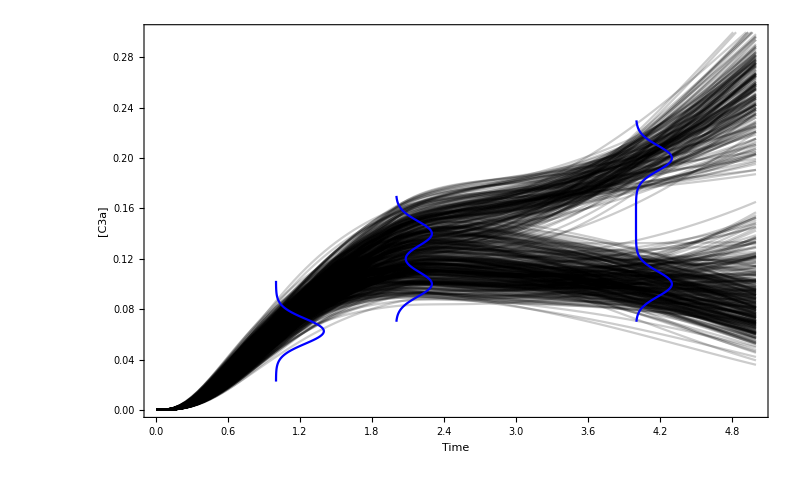

```mathematica
Show[ListLinePlot[data,PlotStyle->Opacity[0.2,Black],Evaluate@options3,FrameLabel->{"Time","[C3a]"},ImageSize->800,PlotRange->{Automatic,{0.,0.3}}],g3]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,0.004],x],{x,-0.02,0.02},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,101}}];
aPlot2=Plot[1/2 (PDF[NormalDistribution[-0.045,0.025],x]+PDF[NormalDistribution[0.045,0.025],x]),{x,-0.12,0.12},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/2,PlotRange->{Automatic,{0,14}}];
aPlot3=Plot[1/2 (PDF[NormalDistribution[-0.05,0.01],x]+PDF[NormalDistribution[0.05,0.01],x]),{x,-0.14,0.14},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,31}}];
aPlot4=Plot[0.5 PDF[NormalDistribution[0,0.005],x],{x,-0.025,0.025},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/4,PlotRange->{Automatic,{0,41}}];
```

```mathematica
g1=Show[ListPlot[Thread[{1,1}],PlotRange->{{0.7,4.5},{0,0.3}},Evaluate@options3,PlotMarkers ->{Automatic,15},FrameLabel->{"Time","[C3a]"},ImageSize->800],Graphics[Inset[Rotate[aPlot1,3Pi /2],{1.22,0.0625}]],Graphics[Inset[Rotate[aPlot2,3Pi /2],{2.32,0.12}]],Graphics[Inset[Rotate[aPlot4,3Pi /2],{4.15,0.2}]],Graphics[Inset[Rotate[aPlot4,3Pi /2],{4.15,0.1}]]]
```

-Graphics-

```mathematica
Show[g1,g3]
```

-Graphics-

```mathematica
g2=Labeled[Show[ListLinePlot[data,PlotStyle->Opacity[0.2,Black],Evaluate@options3,FrameLabel->{"Time","[C3a]"},PlotRange->{Automatic,{0.,0.3}}],g1,ImageSize->600],"A.",{{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

-Graphics-A.

```mathematica
Export["../figures/tnf_samples_vs_distribution.pdf",g2]
```

../figures/tnf_samples_vs_distribution.pdf

## Drawing a plot of posterior samples

```mathematica
samples=Import["../data/tnf_parameters.csv"];
```

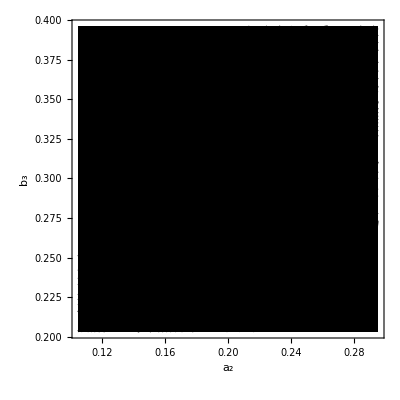
-Graphics-C.

```mathematica
gb=Labeled[SmoothDensityHistogram[samples[[All,{2,7}]],Mesh->20,MeshStyle->Directive[Gray,Dashed],PlotTheme->"Monochrome",Evaluate@options3,FrameLabel->{"a_2","b_3"}],"C.",{{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

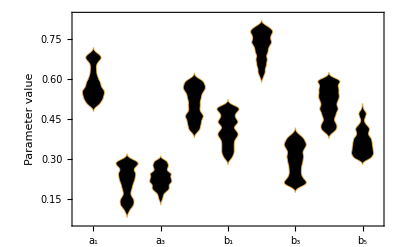
-Graphics-B.

```mathematica
ga=Labeled[DistributionChart[Transpose@samples,ChartLabels->{"a_1","a_2","a_3","a_4","b_1","b_2","b_3","b_4","b_5"},Evaluate@options3,ChartStyle->Black,FrameLabel->{"","Parameter value"}],"B.",{{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

```mathematica
GraphicsRow[{g2,ga,gb},ImageSize->1200,ImagePadding->None]
```

-Graphics-

```mathematica
PositiveSemidefiniteMatrixQ@{{1,2},{2,4}}
```

True

```mathematica
PositiveSemidefiniteMatrixQ
```

```mathematica
PositiveSemidefiniteMatrixQ[m]
```

False